```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"inhom.wl"
```

```mathematica
<<"fourdiff.wl"
```

### EOMs

```mathematica
(* equations of motion, Eq.15-19 in arXiv:0304070 *)
eqf=Derivative[0,1][f][t,x]-(dim-3)((f[t,x] (-1+1/ia2[t,x]))/x);
eqia2=Derivative[0,1][ia2][t,x]-(dim-3)/x+ia2[t,x]*(8(dim-3)+(dim-2)^3*(U[t,x]^2+V[t,x]^2))/(8*x);
eqU=Derivative[0,1][U][t,x]-(f[t,x] ((dim-2-2(dim-3)/ia2[t,x]) U[t,x]+(dim-2)*V[t,x])-2*x*Derivative[1,0][U][t,x])/(2*x*(f[t,x]+x));
eqV=Derivative[0,1][V][t,x]-(f[t,x] ((dim-2-2(dim-3)/ia2[t,x]) V[t,x]+(dim-2)*U[t,x])+2*x*Derivative[1,0][V][t,x])/(2*x*(f[t,x]-x));
constr=Derivative[1,0][ia2][t,x]+dim-3-ia2[t,x]*(dim-3+(dim-2)^3*((x+f[t,x]) U[t,x]^2+(x-f[t,x]) V[t,x]^2)/(8*x));
```

```mathematica
(*EOM from Carsten's paper, for comparison *)
Eq15=-(f[t,x] (-1+1/ia2[t,x]))/x+Derivative[0,1][f][t,x];
Eq16=(-1+ia2[t,x] (1+U[t,x]^2+V[t,x]^2))/x+Derivative[0,1][ia2][t,x];
Eq17=(x-ia2[t,x] (x+(x+f[t,x]) U[t,x]^2+(x-f[t,x]) V[t,x]^2))/x+Derivative[1,0][ia2][t,x];
Eq18=Derivative[0,1][U][t,x]+(f[t,x] ((-1+1/ia2[t,x]) U[t,x]-V[t,x])+x Derivative[1,0][U][t,x])/(x (x+f[t,x]));
Eq19=Derivative[0,1][V][t,x]+(f[t,x] (U[t,x]+(1-1/ia2[t,x]) V[t,x])+x Derivative[1,0][V][t,x])/(x (x-f[t,x]));
```

```mathematica
(*Check whether they match for D=4*)
{Eq15-eqf,Eq16-eqia2,Eq18-eqU,Eq19-eqV,Eq17-constr}/.dim->4//Simplify
```

{0,0,0,0,0}

```mathematica
(* collecting all EOMs *)
EOMall={Eq15==0,Eq16==0,Eq18==0,Eq19==0,Eq17==0};
(* only dynamical equations in x *)
EOMs=EOMall[[;;-2]];
(* constraint equation *)
constraint=EOMall[[-1]];
(* collecting EOMs, multiplying by (1-x) such that the leading order is (1-x)^0. *)
EOMall1={Eq15,Eq16,Eq18,(x-1)Eq19,Eq17};
```

### numeric separate evaluation

```mathematica
upmodes=Xini[[5]]+I*Xini[[6]];
(*Rebuild Fourier series*)
upFourier=Riffle[Join[upmodes,Reverse[Conjugate[upmodes]]],0,{1,-2,2}];
(*Inverse Fourier trafo*)
uplist=Sqrt[Nt]*InverseFourier[upFourier];
duplistdt=fourdiff[uplist,DeltaIni,Nt];
```

```mathematica
replgauge={Subscript[f1, 0]->(1&)}
```

{f1_0→(1&)}

```mathematica
replvalNow={Subscript[u1, 0][t]->uplist,Subscript[u1, 0]'[t]->duplistdt};
```

```mathematica
(* Taylor series ansatz around x=1, because of the numeric integrations this has to be repeated during iterations *)
ord1=3;
ia2ser1[t_,x_]:=Sum[Subscript[ia1, i][t]*(x-1)^i,{i,0,ord1}];
fser1[t_,x_]:=Sum[Subscript[f1, i][t]*(x-1)^i,{i,0,ord1}];
User1[t_,x_]:=Sum[Subscript[u1, i][t]*(x-1)^i,{i,0,ord1}];
Vser1[t_,x_]:=Sum[Subscript[v1, i][t]*(x-1)^i,{i,0,ord1}];
replser1={ia2->ia2ser1,f->fser1,U->User1,V->Vser1};
```

```mathematica
odenow=SeriesCoefficient[EOMall1[[5]]/.replser1/.replgauge,{x,1,0}]
```

1-ia1_0[t] (1+2 u1_0[t]^2)+ia1_0'[t]

```mathematica
coeff1=Coefficient[odenow,Subscript[ia1, 0][t]]/Coefficient[odenow,Subscript[ia1, 0]'[t]]
```

-1-2 u1_0[t]^2

```mathematica
coeff2=(odenow/.{Subscript[ia1, 0][t]->0,Subscript[ia1, 0]'[t]->0})/Coefficient[odenow,Subscript[ia1, 0]'[t]]
```

1

```mathematica
replvalNow=Join[replvalNow,{Subscript[ia1, 0][t]->solinhom[(coeff1/.replvalNow),(coeff2/.replvalNow),DeltaIni,Nt]}];
```

```mathematica
odenow=SeriesCoefficient[EOMall1[[4]]/.replser1/.replgauge,{x,1,0}]
```

(u1_0[t]+(1-1/ia1_0[t]) v1_0[t]+v1_0'[t])/(1-f1_1[t])

```mathematica
coeff1=Coefficient[odenow,Subscript[v1, 0][t]]/Coefficient[odenow,Subscript[v1, 0]'[t]]//Simplify
```

1-1/ia1_0[t]

```mathematica
coeff2=(odenow/.{Subscript[v1, 0][t]->0,Subscript[v1, 0]'[t]->0})/Coefficient[odenow,Subscript[v1, 0]'[t]]//Simplify
```

u1_0[t]

```mathematica
replvalNow=Join[Flatten[replvalNow],{Subscript[v1, 0][t]->solinhom[(coeff1/.replvalNow),(coeff2/.replvalNow),DeltaIni,Nt]}];
```

```mathematica
eomnow=SeriesCoefficient[EOMall1[[1;;3]]/.replser1/.replgauge,{x,1,0}]
```

{1+f1_1[t]-1/ia1_0[t],-1+ia1_1[t]+ia1_0[t] (1+u1_0[t]^2+v1_0[t]^2),u1_1[t]+1/2 ((-1+1/ia1_0[t]) u1_0[t]-v1_0[t]+u1_0'[t])}

```mathematica
Solve[Thread[eomnow==0],{Subscript[ia1, 1][t],Subscript[f1, 1][t],Subscript[u1, 1][t]}]//Simplify
```

{{ia1_1[t]→1-ia1_0[t] (1+u1_0[t]^2+v1_0[t]^2),f1_1[t]→-1+1/ia1_0[t],u1_1[t]→1/2 ((1-1/ia1_0[t]) u1_0[t]+v1_0[t]-u1_0'[t])}}

```mathematica
solNow=Solve[Thread[eomnow==0],{Subscript[ia1, 1][t],Subscript[f1, 1][t],Subscript[u1, 1][t]}]/.replvalNow//Flatten
```

{ia1_1[t]→{0.0814231+6.14524×10^-18 ⅈ,0.0771364+2.89083×10^-17 ⅈ,0.0729059+2.24353×10^-17 ⅈ,0.0687179+1.68983×10^-17 ⅈ,0.0645662+2.17337×10^-18 ⅈ,0.0604523+2.92291×10^-17 ⅈ,0.0563856+7.90349×10^-18 ⅈ,0.0523838-1.62653×10^-18 ⅈ,0.048473+8.60436×10^-18 ⅈ,0.044687+3.38276×10^-17 ⅈ,0.0410676+4.5882×10^-18 ⅈ,0.0376642+2.19278×10^-17 ⅈ,0.0345331+3.86943×10^-18 ⅈ,0.0317368+2.86785×10^-17 ⅈ,0.0293437+3.48907×10^-18 ⅈ,0.0274262-1.15534×10^-18 ⅈ,0.0260601+7.44567×10^-18 ⅈ,0.0253229+2.83248×10^-17 ⅈ,0.0252916-1.52905×10^-19 ⅈ,0.026041-1.08418×10^-17 ⅈ,0.0276411+3.3879×10^-18 ⅈ,0.0301543+5.10864×10^-17 ⅈ,0.0336328-3.61065×10^-18 ⅈ,0.0381148-2.60558×10^-18 ⅈ,0.0436215+3.24452×10^-18 ⅈ,0.0501537+1.57194×10^-17 ⅈ,0.0576881-7.36935×10^-18 ⅈ,0.0661746-1.9147×10^-17 ⅈ,0.0755338+2.06317×10^-18 ⅈ,0.0856547+3.51445×10^-17 ⅈ,0.0963942-3.51717×10^-18 ⅈ,0.107578-4.14088×10^-18 ⅈ,0.119001-8.67744×10^-19 ⅈ,0.130436-4.09886×10^-19 ⅈ,0.141634-3.23284×10^-18 ⅈ,0.152335+6.57524×10^-19 ⅈ,0.162282-2.03121×10^-19 ⅈ,0.171227+5.87402×10^-18 ⅈ,0.178944-1.37384×10^-18 ⅈ,0.185248-6.14088×10^-18 ⅈ,0.189997-2.19724×10^-18 ⅈ,0.193109-3.79446×10^-18 ⅈ,0.19456+2.76615×10^-18 ⅈ,0.194392+2.28577×10^-17 ⅈ,0.192701-1.37258×10^-18 ⅈ,0.189638-1.55262×10^-17 ⅈ,0.18539-5.09899×10^-18 ⅈ,0.18017-4.77493×10^-18 ⅈ,0.174202-1.43527×10^-18 ⅈ,0.167705+4.91222×10^-18 ⅈ,0.160883+5.57469×10^-18 ⅈ,0.153918+3.35915×10^-17 ⅈ,0.146958+6.7856×10^-20 ⅈ,0.140121-1.30411×10^-17 ⅈ,0.133494+1.01733×10^-18 ⅈ,0.12713+1.83332×10^-18 ⅈ,0.121059+2.24476×10^-18 ⅈ,0.115288+1.84656×10^-17 ⅈ,0.109808+1.31651×10^-17 ⅈ,0.104596+2.13922×10^-17 ⅈ,0.0996227+1.12236×10^-18 ⅈ,0.0948535+2.31967×10^-17 ⅈ,0.0902529+7.32899×10^-18 ⅈ,0.0857865-5.28436×10^-19 ⅈ,0.0814231+6.14524×10^-18 ⅈ,0.0771364+2.89083×10^-17 ⅈ,0.0729059+2.24353×10^-17 ⅈ,0.0687179+1.68983×10^-17 ⅈ,0.0645662+2.17337×10^-18 ⅈ,0.0604523+2.92291×10^-17 ⅈ,0.0563856+7.90349×10^-18 ⅈ,0.0523838-1.62653×10^-18 ⅈ,0.048473+8.60436×10^-18 ⅈ,0.044687+3.38276×10^-17 ⅈ,0.0410676+4.5882×10^-18 ⅈ,0.0376642+2.19278×10^-17 ⅈ,0.0345331+3.86943×10^-18 ⅈ,0.0317368+2.86785×10^-17 ⅈ,0.0293437+3.48907×10^-18 ⅈ,0.0274262-1.15534×10^-18 ⅈ,0.0260601+7.44567×10^-18 ⅈ,0.0253229+2.83248×10^-17 ⅈ,0.0252916-1.52905×10^-19 ⅈ,0.026041-1.08418×10^-17 ⅈ,0.0276411+3.3879×10^-18 ⅈ,0.0301543+5.10864×10^-17 ⅈ,0.0336328-3.61065×10^-18 ⅈ,0.0381148-2.60558×10^-18 ⅈ,0.0436215+3.24452×10^-18 ⅈ,0.0501537+1.57194×10^-17 ⅈ,0.0576881-7.36935×10^-18 ⅈ,0.0661746-1.9147×10^-17 ⅈ,0.0755338+2.06317×10^-18 ⅈ,0.0856547+3.51445×10^-17 ⅈ,0.0963942-3.51717×10^-18 ⅈ,0.107578-4.14088×10^-18 ⅈ,0.119001-8.67744×10^-19 ⅈ,0.130436-4.09886×10^-19 ⅈ,0.141634-3.23284×10^-18 ⅈ,0.152335+6.57524×10^-19 ⅈ,0.162282-2.03121×10^-19 ⅈ,0.171227+5.87402×10^-18 ⅈ,0.178944-1.37384×10^-18 ⅈ,0.185248-6.14088×10^-18 ⅈ,0.189997-2.19724×10^-18 ⅈ,0.193109-3.79446×10^-18 ⅈ,0.19456+2.76615×10^-18 ⅈ,0.194392+2.28577×10^-17 ⅈ,0.192701-1.37258×10^-18 ⅈ,0.189638-1.55262×10^-17 ⅈ,0.18539-5.09899×10^-18 ⅈ,0.18017-4.77493×10^-18 ⅈ,0.174202-1.43527×10^-18 ⅈ,0.167705+4.91222×10^-18 ⅈ,0.160883+5.57469×10^-18 ⅈ,0.153918+3.35915×10^-17 ⅈ,0.146958+6.7856×10^-20 ⅈ,0.140121-1.30411×10^-17 ⅈ,0.133494+1.01733×10^-18 ⅈ,0.12713+1.83332×10^-18 ⅈ,0.121059+2.24476×10^-18 ⅈ,0.115288+1.84656×10^-17 ⅈ,0.109808+1.31651×10^-17 ⅈ,0.104596+2.13922×10^-17 ⅈ,0.0996227+1.12236×10^-18 ⅈ,0.0948535+2.31967×10^-17 ⅈ,0.0902529+7.32899×10^-18 ⅈ,0.0857865-5.28436×10^-19 ⅈ},f1_1[t]→{0.46826+9.6621×10^-18 ⅈ,0.460737+1.96134×10^-17 ⅈ,0.452729+1.0241×10^-17 ⅈ,0.444295+8.87744×10^-18 ⅈ,0.435491+9.08641×10^-18 ⅈ,0.426375+1.08495×10^-17 ⅈ,0.417003+2.03533×10^-17 ⅈ,0.40743+9.07382×10^-18 ⅈ,0.397714+1.31394×10^-17 ⅈ,0.387912+2.02386×10^-17 ⅈ,0.378082+6.29114×10^-18 ⅈ,0.368284+8.41859×10^-18 ⅈ,0.35858+3.73911×10^-18 ⅈ,0.349033+4.33822×10^-18 ⅈ,0.339707+1.17381×10^-17 ⅈ,0.330669-4.0031×10^-20 ⅈ,0.321985+8.41286×10^-18 ⅈ,0.313724+9.09338×10^-18 ⅈ,0.305956+4.67541×10^-18 ⅈ,0.298751+7.98285×10^-18 ⅈ,0.292179-4.14939×10^-18 ⅈ,0.286312-1.37282×10^-18 ⅈ,0.281217-1.6001×10^-18 ⅈ,0.276964-1.05963×10^-17 ⅈ,0.273619-5.25311×10^-19 ⅈ,0.271245-6.41233×10^-18 ⅈ,0.269902-5.5629×10^-18 ⅈ,0.269644-4.64743×10^-18 ⅈ,0.270519-1.0073×10^-17 ⅈ,0.272568-7.84359×10^-18 ⅈ,0.275819-1.30311×10^-17 ⅈ,0.280292-1.28103×10^-17 ⅈ,0.28599-9.38405×10^-18 ⅈ,0.2929-1.85254×10^-17 ⅈ,0.300991-8.88352×10^-18 ⅈ,0.310208-1.01295×10^-17 ⅈ,0.320477-9.96691×10^-18 ⅈ,0.331694-8.35162×10^-18 ⅈ,0.343734-1.79952×10^-17 ⅈ,0.356446-1.00794×10^-17 ⅈ,0.369656-1.40055×10^-17 ⅈ,0.383171-2.05501×10^-17 ⅈ,0.396782-7.33022×10^-18 ⅈ,0.410277-8.62199×10^-18 ⅈ,0.423437-3.06654×10^-18 ⅈ,0.436056-4.62989×10^-18 ⅈ,0.44794-1.21789×10^-17 ⅈ,0.458918-4.38892×10^-20 ⅈ,0.468844-1.10369×10^-17 ⅈ,0.477606-1.02782×10^-17 ⅈ,0.485121-4.98827×10^-18 ⅈ,0.491339-6.35577×10^-18 ⅈ,0.49624+5.57759×10^-18 ⅈ,0.49983+1.00109×10^-18 ⅈ,0.502136+3.33557×10^-18 ⅈ,0.503203+1.36027×10^-17 ⅈ,0.50309-6.19957×10^-19 ⅈ,0.501863+7.1623×10^-18 ⅈ,0.499595+8.14655×10^-18 ⅈ,0.49636+5.53562×10^-18 ⅈ,0.492233+1.01343×10^-17 ⅈ,0.48729+1.04448×10^-17 ⅈ,0.481601+1.75799×10^-17 ⅈ,0.475235+1.41923×10^-17 ⅈ,0.46826+9.6621×10^-18 ⅈ,0.460737+1.96134×10^-17 ⅈ,0.452729+1.0241×10^-17 ⅈ,0.444295+8.87744×10^-18 ⅈ,0.435491+9.08641×10^-18 ⅈ,0.426375+1.08495×10^-17 ⅈ,0.417003+2.03533×10^-17 ⅈ,0.40743+9.07382×10^-18 ⅈ,0.397714+1.31394×10^-17 ⅈ,0.387912+2.02386×10^-17 ⅈ,0.378082+6.29114×10^-18 ⅈ,0.368284+8.41859×10^-18 ⅈ,0.35858+3.73911×10^-18 ⅈ,0.349033+4.33822×10^-18 ⅈ,0.339707+1.17381×10^-17 ⅈ,0.330669-4.0031×10^-20 ⅈ,0.321985+8.41286×10^-18 ⅈ,0.313724+9.09338×10^-18 ⅈ,0.305956+4.67541×10^-18 ⅈ,0.298751+7.98285×10^-18 ⅈ,0.292179-4.14939×10^-18 ⅈ,0.286312-1.37282×10^-18 ⅈ,0.281217-1.6001×10^-18 ⅈ,0.276964-1.05963×10^-17 ⅈ,0.273619-5.25311×10^-19 ⅈ,0.271245-6.41233×10^-18 ⅈ,0.269902-5.5629×10^-18 ⅈ,0.269644-4.64743×10^-18 ⅈ,0.270519-1.0073×10^-17 ⅈ,0.272568-7.84359×10^-18 ⅈ,0.275819-1.30311×10^-17 ⅈ,0.280292-1.28103×10^-17 ⅈ,0.28599-9.38405×10^-18 ⅈ,0.2929-1.85254×10^-17 ⅈ,0.300991-8.88352×10^-18 ⅈ,0.310208-1.01295×10^-17 ⅈ,0.320477-9.96691×10^-18 ⅈ,0.331694-8.35162×10^-18 ⅈ,0.343734-1.79952×10^-17 ⅈ,0.356446-1.00794×10^-17 ⅈ,0.369656-1.40055×10^-17 ⅈ,0.383171-2.05501×10^-17 ⅈ,0.396782-7.33022×10^-18 ⅈ,0.410277-8.62199×10^-18 ⅈ,0.423437-3.06654×10^-18 ⅈ,0.436056-4.62989×10^-18 ⅈ,0.44794-1.21789×10^-17 ⅈ,0.458918-4.38892×10^-20 ⅈ,0.468844-1.10369×10^-17 ⅈ,0.477606-1.02782×10^-17 ⅈ,0.485121-4.98827×10^-18 ⅈ,0.491339-6.35577×10^-18 ⅈ,0.49624+5.57759×10^-18 ⅈ,0.49983+1.00109×10^-18 ⅈ,0.502136+3.33557×10^-18 ⅈ,0.503203+1.36027×10^-17 ⅈ,0.50309-6.19957×10^-19 ⅈ,0.501863+7.1623×10^-18 ⅈ,0.499595+8.14655×10^-18 ⅈ,0.49636+5.53562×10^-18 ⅈ,0.492233+1.01343×10^-17 ⅈ,0.48729+1.04448×10^-17 ⅈ,0.481601+1.75799×10^-17 ⅈ,0.475235+1.41923×10^-17 ⅈ},u1_1[t]→{-0.119082+2.38398×10^-15 ⅈ,-0.109107-2.64969×10^-15 ⅈ,-0.0998849+2.92786×10^-15 ⅈ,-0.0912205-2.33122×10^-15 ⅈ,-0.0829298+2.34302×10^-15 ⅈ,-0.0748406-2.70228×10^-15 ⅈ,-0.066794+2.60171×10^-15 ⅈ,-0.0586446-2.04364×10^-15 ⅈ,-0.05026+2.15356×10^-15 ⅈ,-0.0415212-2.55803×10^-15 ⅈ,-0.0323207+2.12618×10^-15 ⅈ,-0.0225627-1.21025×10^-15 ⅈ,-0.0121612+1.65016×10^-15 ⅈ,-0.0010394-6.46442×10^-16 ⅈ,0.0108709+3.12963×10^-16 ⅈ,0.0236306-1.29075×10^-15 ⅈ,0.037294+1.67081×10^-15 ⅈ,0.0519091-1.69684×10^-15 ⅈ,0.0675186+2.77489×10^-17 ⅈ,0.0841603-3.20177×10^-16 ⅈ,0.101866+4.76021×10^-15 ⅈ,0.120663-3.84028×10^-15 ⅈ,0.140568-1.45484×10^-16 ⅈ,0.161593+1.35478×10^-16 ⅈ,0.183733+1.12141×10^-15 ⅈ,0.206972-1.61949×10^-15 ⅈ,0.23127+2.18514×10^-16 ⅈ,0.256565+9.35896×10^-16 ⅈ,0.28276+1.35366×10^-15 ⅈ,0.309723+5.82139×10^-17 ⅈ,0.337272-2.71105×10^-15 ⅈ,0.365171+1.43038×10^-15 ⅈ,0.393123-4.99191×10^-16 ⅈ,0.420764+7.02077×10^-16 ⅈ,0.447662-2.95239×10^-15 ⅈ,0.473318+1.68376×10^-15 ⅈ,0.497173+4.60396×10^-15 ⅈ,0.518627-2.88269×10^-15 ⅈ,0.537059-2.91448×10^-15 ⅈ,0.551859+2.61231×10^-15 ⅈ,0.562468-1.00689×10^-15 ⅈ,0.568419+5.41873×10^-16 ⅈ,0.569378-1.56494×10^-15 ⅈ,0.565183+3.00686×10^-15 ⅈ,0.555867-1.22436×10^-15 ⅈ,0.541667+1.31413×10^-15 ⅈ,0.523019-3.73131×10^-15 ⅈ,0.500528+3.17422×10^-15 ⅈ,0.474926-2.48878×10^-15 ⅈ,0.447025+2.86973×10^-15 ⅈ,0.417659-4.26908×10^-15 ⅈ,0.387631+2.8128×10^-15 ⅈ,0.357675+1.32681×10^-15 ⅈ,0.328417+1.40237×10^-16 ⅈ,0.300366-3.871×10^-15 ⅈ,0.273898+3.02308×10^-15 ⅈ,0.249269-1.73991×10^-15 ⅈ,0.226618+1.72064×10^-15 ⅈ,0.205988-2.1508×10^-15 ⅈ,0.187343+3.60678×10^-15 ⅈ,0.170582-3.60283×10^-15 ⅈ,0.155562+1.67897×10^-15 ⅈ,0.142103-2.03486×10^-15 ⅈ,0.130012+2.58726×10^-15 ⅈ,0.119082-2.38398×10^-15 ⅈ,0.109107+2.64969×10^-15 ⅈ,0.0998849-2.92786×10^-15 ⅈ,0.0912205+2.33122×10^-15 ⅈ,0.0829298-2.34302×10^-15 ⅈ,0.0748406+2.70228×10^-15 ⅈ,0.066794-2.60171×10^-15 ⅈ,0.0586446+2.04364×10^-15 ⅈ,0.05026-2.15356×10^-15 ⅈ,0.0415212+2.55803×10^-15 ⅈ,0.0323207-2.12618×10^-15 ⅈ,0.0225627+1.21025×10^-15 ⅈ,0.0121612-1.65016×10^-15 ⅈ,0.0010394+6.46442×10^-16 ⅈ,-0.0108709-3.12963×10^-16 ⅈ,-0.0236306+1.29075×10^-15 ⅈ,-0.037294-1.67081×10^-15 ⅈ,-0.0519091+1.69684×10^-15 ⅈ,-0.0675186-2.77489×10^-17 ⅈ,-0.0841603+3.20177×10^-16 ⅈ,-0.101866-4.76021×10^-15 ⅈ,-0.120663+3.84028×10^-15 ⅈ,-0.140568+1.45484×10^-16 ⅈ,-0.161593-1.35478×10^-16 ⅈ,-0.183733-1.12141×10^-15 ⅈ,-0.206972+1.61949×10^-15 ⅈ,-0.23127-2.18514×10^-16 ⅈ,-0.256565-9.35896×10^-16 ⅈ,-0.28276-1.35366×10^-15 ⅈ,-0.309723-5.82139×10^-17 ⅈ,-0.337272+2.71105×10^-15 ⅈ,-0.365171-1.43038×10^-15 ⅈ,-0.393123+4.99191×10^-16 ⅈ,-0.420764-7.02077×10^-16 ⅈ,-0.447662+2.95239×10^-15 ⅈ,-0.473318-1.68376×10^-15 ⅈ,-0.497173-4.60396×10^-15 ⅈ,-0.518627+2.88269×10^-15 ⅈ,-0.537059+2.91448×10^-15 ⅈ,-0.551859-2.61231×10^-15 ⅈ,-0.562468+1.00689×10^-15 ⅈ,-0.568419-5.41873×10^-16 ⅈ,-0.569378+1.56494×10^-15 ⅈ,-0.565183-3.00686×10^-15 ⅈ,-0.555867+1.22436×10^-15 ⅈ,-0.541667-1.31413×10^-15 ⅈ,-0.523019+3.73131×10^-15 ⅈ,-0.500528-3.17422×10^-15 ⅈ,-0.474926+2.48878×10^-15 ⅈ,-0.447025-2.86973×10^-15 ⅈ,-0.417659+4.26908×10^-15 ⅈ,-0.387631-2.8128×10^-15 ⅈ,-0.357675-1.32681×10^-15 ⅈ,-0.328417-1.40237×10^-16 ⅈ,-0.300366+3.871×10^-15 ⅈ,-0.273898-3.02308×10^-15 ⅈ,-0.249269+1.73991×10^-15 ⅈ,-0.226618-1.72064×10^-15 ⅈ,-0.205988+2.1508×10^-15 ⅈ,-0.187343-3.60678×10^-15 ⅈ,-0.170582+3.60283×10^-15 ⅈ,-0.155562-1.67897×10^-15 ⅈ,-0.142103+2.03486×10^-15 ⅈ,-0.130012-2.58726×10^-15 ⅈ}}

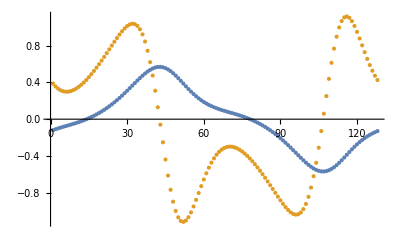

```mathematica
ListPlot[{Re[Subscript[u1, 1][t]/.replvalNow],Re[Subscript[u1, 1]'[t]/.replvalNow]}]
```

```mathematica
replvalNow=Join[replvalNow,solNow];
```

```mathematica
dreplvalNow={};
```

```mathematica
Do[dkey=D[replvalNow[[i,1]],t];
dval=fourdiff[replvalNow[[i,2]],DeltaIni,Nt];
dreplvalNow=Join[dreplvalNow,{dkey->dval}];
,{i,1,Length[replvalNow]}]
```

```mathematica
replvalNow
```

```mathematica
replvalNow=Join[replvalNow,dreplvalNow];
```

```mathematica
(*i=1*)
EOMnow=SeriesCoefficient[EOMall1/.replser1/.replgauge,{x,1,1}];
```

```mathematica
solNow=Flatten[Solve[Thread[EOMnow[[1;;3]]==0]/.replgauge,{Subscript[ia1, 2][t],Subscript[f1, 2][t],Subscript[u1, 2][t]}]]
```

{ia1_2[t]→1/2 (-1+ia1_0[t]-ia1_1[t]+ia1_0[t] u1_0[t]^2-ia1_1[t] u1_0[t]^2-2 ia1_0[t] u1_0[t] u1_1[t]+ia1_0[t] v1_0[t]^2-ia1_1[t] v1_0[t]^2-2 ia1_0[t] v1_0[t] v1_1[t]),f1_2[t]→(-ia1_0[t]+f1_1[t] ia1_0[t]+ia1_0[t]^2-f1_1[t] ia1_0[t]^2-ia1_1[t])/(2 ia1_0[t]^2),u1_2[t]→1/(8 ia1_0[t]^2)(3 ia1_0[t] u1_0[t]-f1_1[t] ia1_0[t] u1_0[t]-3 ia1_0[t]^2 u1_0[t]+f1_1[t] ia1_0[t]^2 u1_0[t]+2 ia1_1[t] u1_0[t]-2 ia1_0[t] u1_1[t]+2 ia1_0[t]^2 u1_1[t]-3 ia1_0[t]^2 v1_0[t]+f1_1[t] ia1_0[t]^2 v1_0[t]+2 ia1_0[t]^2 v1_1[t]+ia1_0[t]^2 u1_0'[t]+f1_1[t] ia1_0[t]^2 u1_0'[t]-2 ia1_0[t]^2 u1_1'[t])}

```mathematica
odenow=EOMnow[[4]]/.replgauge/.solNow//Simplify
```

v1_1[t]+(((-1+f1_1[t]) ia1_0[t]+(-1+f1_1[t]) ia1_0[t]^2-ia1_1[t]) (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]+v1_0'[t])))/(2 (-1+f1_1[t])^2 ia1_0[t]^3)+(u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+f1_1[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(1-1/ia1_0[t]) v1_1[t]+v1_0'[t]+v1_1'[t])/(1-f1_1[t])

```mathematica
coeff1=Coefficient[odenow,Subscript[v1, 1][t]]/Coefficient[odenow,Subscript[v1, 1]'[t]]//Simplify
```

2-f1_1[t]-1/ia1_0[t]

```mathematica
coeff2=(odenow/.{Subscript[v1, 1][t]->0,Subscript[v1, 1]'[t]->0})/Coefficient[odenow,Subscript[v1, 1]'[t]]/.Subscript[ia1, 0][t]->1/(1+Subscript[f1, 1][t])//FullSimplify
```

((2-3 f1_1[t]+f1_1[t]^2+(1+f1_1[t])^2 ia1_1[t]) u1_0[t]+2 (-1+f1_1[t]) u1_1[t]+(-((-1+f1_1[t]) f1_1[t])+(1+f1_1[t])^2 ia1_1[t]) ((-2+f1_1[t]) v1_0[t]+v1_0'[t]))/(2 (-1+f1_1[t]))

```mathematica
replvalNow=Join[Flatten[replvalNow],{Subscript[v1, 1][t]->solinhom[(coeff1/.replvalNow),(coeff2/.replvalNow),DeltaIni,Nt]}];
```

```mathematica
replvalNow=Join[replvalNow,solNow/.replvalNow];
```

```mathematica
dreplvalNow={};
```

```mathematica
Do[dkey=D[replvalNow[[i,1]],t];
dval=fourdiff[replvalNow[[i,2]],DeltaIni,Nt];
dreplvalNow=Join[dreplvalNow,{dkey->dval}];
,{i,-4,-1}]
```

```mathematica
replvalNow=Join[replvalNow,dreplvalNow];
```

```mathematica
Max[Abs[EOMnow/.replgauge/.solNow/.replvalNow]]
```

1.69002×10^-14

```mathematica
(*i=2*)
EOMnow=SeriesCoefficient[EOMall1/.replser1/.replgauge,{x,1,2}];
```

```mathematica
solNow=Flatten[Solve[Thread[EOMnow[[1;;3]]==0]/.replgauge,{Subscript[ia1, 3][t],Subscript[f1, 3][t],Subscript[u1, 3][t]}]];
```

```mathematica
odenow=EOMnow[[4]]/.replgauge/.solNow//Simplify
```

2 v1_2[t]-1/(3 (-1+f1_1[t])^3 ia1_0[t]^4)((-1+f1_1[t]) (-1+f1_1[t]-f1_2[t]) ia1_0[t]^2+(2+2 f1_1[t]^2+4 f1_1[t] (-1+f1_2[t])-4 f1_2[t]+3 f1_2[t]^2) ia1_0[t]^3-(-1+f1_1[t]) ia1_1[t]^2+(-1+f1_1[t]) ia1_0[t] ((-1+f1_1[t]) ia1_1[t]+ia1_2[t])) (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]+v1_0'[t]))+((-1+f1_1[t]+f1_2[t]) (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+f1_1[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(1-1/ia1_0[t]) v1_1[t]+v1_0'[t]+v1_1'[t]))/(-1+f1_1[t])^2+(u1_2[t]+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+f1_2[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(ia1_1[t] v1_1[t])/ia1_0[t]^2+f1_1[t] (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_1[t])+(1-1/ia1_0[t]) v1_2[t]+v1_1'[t]+v1_2'[t])/(1-f1_1[t])

```mathematica
coeff1=Coefficient[odenow,Subscript[v1, 2][t]]/Coefficient[odenow,Subscript[v1, 2]'[t]]//Simplify
```

3-2 f1_1[t]-1/ia1_0[t]

```mathematica
coeff2=(odenow/.{Subscript[v1, 2][t]->0,Subscript[v1, 2]'[t]->0})/Coefficient[odenow,Subscript[v1, 2]'[t]]//Simplify
```

(1-f1_1[t]) (-1/(3 (-1+f1_1[t])^3 ia1_0[t]^4)((-1+f1_1[t]) (-1+f1_1[t]-f1_2[t]) ia1_0[t]^2+(2+2 f1_1[t]^2+4 f1_1[t] (-1+f1_2[t])-4 f1_2[t]+3 f1_2[t]^2) ia1_0[t]^3-(-1+f1_1[t]) ia1_1[t]^2+(-1+f1_1[t]) ia1_0[t] ((-1+f1_1[t]) ia1_1[t]+ia1_2[t])) (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]+v1_0'[t]))+(u1_2[t]+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+f1_2[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(ia1_1[t] v1_1[t])/ia1_0[t]^2+f1_1[t] (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_1[t])+v1_1'[t])/(1-f1_1[t])+((-1+f1_1[t]+f1_2[t]) (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+f1_1[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(1-1/ia1_0[t]) v1_1[t]+v1_0'[t]+v1_1'[t]))/(-1+f1_1[t])^2)

```mathematica
replvalNow=Join[Flatten[replvalNow],{Subscript[v1, 2][t]->solinhom[(coeff1/.replvalNow),(coeff2/.replvalNow),DeltaIni,Nt]}];
```

```mathematica
replvalNow=Join[replvalNow,solNow/.replvalNow];
```

```mathematica
dreplvalNow={};
```

```mathematica
Do[dkey=D[replvalNow[[i,1]],t];
dval=fourdiff[replvalNow[[i,2]],DeltaIni,Nt];
dreplvalNow=Join[dreplvalNow,{dkey->dval}];
,{i,-4,-1}]
```

```mathematica
replvalNow=Join[replvalNow,dreplvalNow];
```

```mathematica
Max[Abs[EOMnow/.replgauge/.solNow/.replvalNow]]
```

3.31676×10^-14

```mathematica
(*i=3*)
EOMnow=SeriesCoefficient[EOMall1/.replser1/.replgauge,{x,1,3}];
```

```mathematica
solNow=Flatten[Solve[Thread[EOMnow[[1;;3]]==0]/.replgauge,{Subscript[ia1, 4][t],Subscript[f1, 4][t],Subscript[u1, 4][t]}]];
```

```mathematica
odenow=EOMnow[[4]]/.replgauge/.solNow//Simplify
```

3 v1_3[t]+((-1+f1_1[t]^3-f1_2[t]^2+f1_2[t]^3+f1_1[t]^2 (-3+f1_2[t]-f1_3[t])-f1_3[t]+f1_2[t] (1+2 f1_3[t])+f1_1[t] (3+f1_2[t]^2+2 f1_3[t]-2 f1_2[t] (1+f1_3[t]))) (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]+v1_0'[t])))/((-1+f1_1[t])^4 ia1_0[t])-((1+f1_1[t]^2-f1_2[t]+f1_2[t]^2+f1_1[t] (-2+f1_2[t]-f1_3[t])+f1_3[t]) (ia1_1[t] v1_0[t]+f1_1[t] ia1_0[t] (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]))-ia1_0[t] v1_1[t]+ia1_0[t]^2 (u1_1[t]+v1_1[t]+v1_0'[t]+v1_1'[t])))/((-1+f1_1[t])^3 ia1_0[t]^2)+((-1+f1_1[t]+f1_2[t]) (u1_2[t]+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+f1_2[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(ia1_1[t] v1_1[t])/ia1_0[t]^2+f1_1[t] (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_1[t])+(1-1/ia1_0[t]) v1_2[t]+v1_1'[t]+v1_2'[t]))/(-1+f1_1[t])^2+1/(1-f1_1[t])(u1_3[t]+((ia1_1[t]^3-2 ia1_0[t] ia1_1[t] ia1_2[t]+ia1_0[t]^2 ia1_3[t]) v1_0[t])/ia1_0[t]^4+f1_3[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_1[t])/ia1_0[t]^3+f1_2[t] (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_1[t])+(ia1_1[t] v1_2[t])/ia1_0[t]^2+f1_1[t] (u1_2[t]+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+(ia1_1[t] v1_1[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_2[t])+(1-1/ia1_0[t]) v1_3[t]+v1_2'[t]+v1_3'[t])

```mathematica
coeff1=Coefficient[odenow,Subscript[v1, 3][t]]/Coefficient[odenow,Subscript[v1, 3]'[t]]//Simplify
```

4-3 f1_1[t]-1/ia1_0[t]

```mathematica
coeff2=(odenow/.{Subscript[v1, 3][t]->0,Subscript[v1, 3]'[t]->0})/Coefficient[odenow,Subscript[v1, 3]'[t]]//Simplify
```

(1-f1_1[t]) (((-1+f1_1[t]^3-f1_2[t]^2+f1_2[t]^3+f1_1[t]^2 (-3+f1_2[t]-f1_3[t])-f1_3[t]+f1_2[t] (1+2 f1_3[t])+f1_1[t] (3+f1_2[t]^2+2 f1_3[t]-2 f1_2[t] (1+f1_3[t]))) (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]+v1_0'[t])))/((-1+f1_1[t])^4 ia1_0[t])-((1+f1_1[t]^2-f1_2[t]+f1_2[t]^2+f1_1[t] (-2+f1_2[t]-f1_3[t])+f1_3[t]) (ia1_1[t] v1_0[t]+f1_1[t] ia1_0[t] (-v1_0[t]+ia1_0[t] (u1_0[t]+v1_0[t]))-ia1_0[t] v1_1[t]+ia1_0[t]^2 (u1_1[t]+v1_1[t]+v1_0'[t]+v1_1'[t])))/((-1+f1_1[t])^3 ia1_0[t]^2)+1/(1-f1_1[t])(u1_3[t]+((ia1_1[t]^3-2 ia1_0[t] ia1_1[t] ia1_2[t]+ia1_0[t]^2 ia1_3[t]) v1_0[t])/ia1_0[t]^4+f1_3[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_1[t])/ia1_0[t]^3+f1_2[t] (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_1[t])+(ia1_1[t] v1_2[t])/ia1_0[t]^2+f1_1[t] (u1_2[t]+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+(ia1_1[t] v1_1[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_2[t])+v1_2'[t])+((-1+f1_1[t]+f1_2[t]) (u1_2[t]+((-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+f1_2[t] (u1_0[t]+(1-1/ia1_0[t]) v1_0[t])+(ia1_1[t] v1_1[t])/ia1_0[t]^2+f1_1[t] (u1_1[t]+(ia1_1[t] v1_0[t])/ia1_0[t]^2+(1-1/ia1_0[t]) v1_1[t])+(1-1/ia1_0[t]) v1_2[t]+v1_1'[t]+v1_2'[t]))/(-1+f1_1[t])^2)

```mathematica
replvalNow=Join[Flatten[replvalNow],{Subscript[v1, 3][t]->solinhom[(coeff1/.replvalNow),(coeff2/.replvalNow),DeltaIni,Nt]}];
```

```mathematica
replvalNow=Join[replvalNow,solNow/.replvalNow];
```

```mathematica
dreplvalNow={};
```

```mathematica
Do[dkey=D[replvalNow[[i,1]],t];
dval=fourdiff[replvalNow[[i,2]],DeltaIni,Nt];
dreplvalNow=Join[dreplvalNow,{dkey->dval}];
,{i,-4,-1}]
```

```mathematica
replvalNow=Join[replvalNow,dreplvalNow];
```

#### Check whether this solves the EOM to specified order

```mathematica
(* Order (x-1)^-1 *)
```

```mathematica
Max[Abs[SeriesCoefficient[{Eq15,Eq16,Eq17,Eq18,Eq19}/.replser1/.replgauge/.replvalNow,{x,1,-1}]]]
```

1.5431×10^-14

```mathematica
(* Order (x-1)^0 *)
```

```mathematica
Max[Abs[SeriesCoefficient[{Eq15,Eq16,Eq17,Eq18,Eq19}/.replser1/.replgauge/.replvalNow,{x,1,0}]]]
```

1.59041×10^-14

```mathematica
(* Order (x-1)^1 *)
```

```mathematica
Max[Abs[SeriesCoefficient[{Eq15,Eq16,Eq17,Eq18,Eq19}/.replser1/.replgauge/.replvalNow,{x,1,1}]]]
```

1.69123×10^-14

```mathematica
(* Order (x-1)^2 *)
```

```mathematica
Max[Abs[SeriesCoefficient[{Eq15,Eq16,Eq17,Eq18,Eq19}/.replser1/.replgauge/.replvalNow,{x,1,2}]]]
```

1.17177×10^-13

### Perturbative analysis around x=0 (loop)

```mathematica
(* Taylor series ansatz around x=0 *)
ord0=3;
ia2ser0[t_,x_]:=Sum[Subscript[ia0, i][t]*x^i,{i,0,ord0}];
fser0[t_,x_]:=Sum[Subscript[f0, i][t]*x^i,{i,0,ord0}];
User0[t_,x_]:=Sum[Subscript[u0, i][t]*x^i,{i,0,ord0}];
Vser0[t_,x_]:=Sum[Subscript[v0, i][t]*x^i,{i,0,ord0}];
replser0={ia2->ia2ser0,f->fser0,U->User0,V->Vser0};
```

```mathematica
(* boundary conditions: ia2=1 and f is keept generic *)
replBC0={Subscript[f0, 0]->fBC0,Subscript[ia0, 0]->(1&),Subscript[u0, 1]->uBC0};
```

```mathematica
replBC0={Subscript[ia0, 0]->(1&)};
```

```mathematica
(* collecting EOMs, multiplying by x such that the leading order is x^0. *)
EOMall0=x*{eqf,eqia2,eqU,eqV,constr};
```

```mathematica
(* solving EOMs order by order *)
replsol0=replBC0;
Do[
(* expanding EOMs to given order *)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,i}];
(* solving for series coefficients *)
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[f0, i][t],Subscript[ia0, i][t],Subscript[u0, i][t],Subscript[v0, i][t]}]//Flatten//FullSimplify;
(* replacement rule for derivatives *)
dtsolNow=D[solNow,t];
(* adding solution to replacement rule *)
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
(* checking if solution satisfies constraint *)
checkNow=0==EOMnow[[-1]]/.replser0/.replsol0;
Print["order: ",i,", ",checkNow,", ",solNow];
,{i,0,ord0}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

order: 0, True, {u0_0[t]→0,v0_0[t]→0}

Solve::svars: Equations may not give solutions for all "solve" variables.

order: 1, True, {f0_1[t]→0,ia0_1[t]→0,v0_1[t]→u0_1[t]}

order: 2, True, {f0_2[t]→((-3+dim) (-2+dim)^3 f0_0[t] u0_1[t]^2)/(8 (-1+dim)),ia0_2[t]→-((-2+dim)^3 u0_1[t]^2)/(4 (-1+dim)),u0_2[t]→(u0_1[t]+u0_1'[t])/(f0_0[t]-dim f0_0[t]),v0_2[t]→(u0_1[t]+u0_1'[t])/((-1+dim) f0_0[t])}

order: 3, True, {f0_3[t]→0,ia0_3[t]→0,u0_3[t]→-1/(8 (-1+dim) f0_0[t]^3)((-3+dim) (-2+dim)^3 f0_0[t]^3 u0_1[t]^3+4 f0_0'[t] (u0_1[t]+u0_1'[t])-4 f0_0[t] (2 u0_1[t]+3 u0_1'[t]+u0_1''[t])),v0_3[t]→-1/(8 (-1+dim) f0_0[t]^3)((-3+dim) (-2+dim)^3 f0_0[t]^3 u0_1[t]^3+4 f0_0'[t] (u0_1[t]+u0_1'[t])-4 f0_0[t] (2 u0_1[t]+3 u0_1'[t]+u0_1''[t]))}

```mathematica
(* exporting series solution to file *)
SetDirectory[NotebookDirectory[]];
Put[replsol0,"pertSol0ord5.res"];
```

### Perturbative analysis around x=0

```mathematica
(* Taylor series ansatz around x=0 *)
ord0=4;
ia2ser0[t_,x_]:=Sum[Subscript[ia0, i][t]*x^i,{i,0,ord0}];
fser0[t_,x_]:=Sum[Subscript[f0, i][t]*x^i,{i,0,ord0}];
User0[t_,x_]:=Sum[Subscript[u0, i][t]*x^i,{i,0,ord0}];
Vser0[t_,x_]:=Sum[Subscript[v0, i][t]*x^i,{i,0,ord0}];
replser0={ia2->ia2ser0,f->fser0,U->User0,V->Vser0};
```

```mathematica
(* boundary conditions: ia2=1 and f is keept generic *)
replBC0={Subscript[f0, 0]->fBC0,Subscript[ia0, 0]->(1&),Subscript[u0, 1]->uBC0};
```

```mathematica
replBC0={Subscript[ia0, 0]->(1&)};
```

```mathematica
(* collecting EOMs, multiplying by x such that the leading order is x^0. *)
EOMall0={eqf,eqia2,eqU,eqV,constr};
```

```mathematica
replsol0=replBC0;
```

```mathematica
(*ORDER 0*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,-1}]//FullSimplify
```

{0,1/8 (-2+dim)^3 (u0_0[t]^2+v0_0[t]^2),1/2 ((-4+dim) u0_0[t]-(-2+dim) v0_0[t]),1/2 (-((-2+dim) u0_0[t])+(-4+dim) v0_0[t]),-1/8 (-2+dim)^3 f0_0[t] (u0_0[t]^2-v0_0[t]^2)}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[f0, 0][t],Subscript[ia0, 0][t],Subscript[u0, 0][t],Subscript[v0, 0][t]}]//Flatten//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{u0_0[t]→0,v0_0[t]→0}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%
```

{0,0,0,0,0}

```mathematica
(*ORDER 1*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,0}]//FullSimplify
```

{f0_1[t]+(-3+dim) f0_0[t] ia0_1[t],(-2+dim) ia0_1[t],1/2 (-2+dim) (u0_1[t]-v0_1[t]),1/2 (-2+dim) (-u0_1[t]+v0_1[t]),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[f0, 1][t],Subscript[ia0, 1][t],Subscript[u0, 1][t],Subscript[v0, 1][t]}]//Flatten//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{f0_1[t]→0,ia0_1[t]→0,v0_1[t]→u0_1[t]}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%
```

{0,0,0,0,0}

```mathematica
(*ORDER 2*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,1}]//FullSimplify
```

{2 f0_2[t]+(-3+dim) f0_0[t] ia0_2[t],(-1+dim) ia0_2[t]+1/4 (-2+dim)^3 u0_1[t]^2,(2 u0_1[t]+f0_0[t] (dim u0_2[t]-(-2+dim) v0_2[t])+2 u0_1'[t])/(2 f0_0[t]),(-2 u0_1[t]+f0_0[t] (-((-2+dim) u0_2[t])+dim v0_2[t])-2 u0_1'[t])/(2 f0_0[t]),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[f0, 2][t],Subscript[ia0, 2][t],Subscript[u0, 2][t],Subscript[v0, 2][t]}]//Flatten//FullSimplify
```

{f0_2[t]→((-3+dim) (-2+dim)^3 f0_0[t] u0_1[t]^2)/(8 (-1+dim)),ia0_2[t]→-((-2+dim)^3 u0_1[t]^2)/(4 (-1+dim)),u0_2[t]→(u0_1[t]+u0_1'[t])/(f0_0[t]-dim f0_0[t]),v0_2[t]→(u0_1[t]+u0_1'[t])/((-1+dim) f0_0[t])}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%//Simplify
```

{0,0,0,0,0}

```mathematica
(*ORDER 3*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,2}]//FullSimplify
```

{3 f0_3[t]+(-3+dim) f0_0[t] ia0_3[t],dim ia0_3[t],1/(4 (-1+dim) f0_0[t]^3)(f0_0[t]^3 ((-3+dim) (-2+dim)^3 u0_1[t]^3+2 (-1+dim) ((2+dim) u0_3[t]-(-2+dim) v0_3[t]))+4 f0_0'[t] (u0_1[t]+u0_1'[t])-4 f0_0[t] (2 u0_1[t]+3 u0_1'[t]+u0_1''[t])),1/(4 (-1+dim) f0_0[t]^3)(f0_0[t]^3 ((-3+dim) (-2+dim)^3 u0_1[t]^3+2 (-1+dim) (-((-2+dim) u0_3[t])+(2+dim) v0_3[t]))+4 f0_0'[t] (u0_1[t]+u0_1'[t])-4 f0_0[t] (2 u0_1[t]+3 u0_1'[t]+u0_1''[t])),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[f0, 3][t],Subscript[ia0, 3][t],Subscript[u0, 3][t],Subscript[v0, 3][t]}]//Flatten//FullSimplify
```

{f0_3[t]→0,ia0_3[t]→0,u0_3[t]→-1/(8 (-1+dim) f0_0[t]^3)((-3+dim) (-2+dim)^3 f0_0[t]^3 u0_1[t]^3+4 f0_0'[t] (u0_1[t]+u0_1'[t])-4 f0_0[t] (2 u0_1[t]+3 u0_1'[t]+u0_1''[t])),v0_3[t]→-1/(8 (-1+dim) f0_0[t]^3)((-3+dim) (-2+dim)^3 f0_0[t]^3 u0_1[t]^3+4 f0_0'[t] (u0_1[t]+u0_1'[t])-4 f0_0[t] (2 u0_1[t]+3 u0_1'[t]+u0_1''[t]))}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%//Simplify
```

{0,0,0,0,0}

### Perturbative analysis around x = 1

```mathematica
replgauge={Subscript[f1, 0]->(1&)}
```

{f1_0→(1&)}

```mathematica
(* Taylor series ansatz around x=1, because of the numeric integrations this has to be repeated during iterations *)
ord1=2;
ia2ser1[t_,x_]:=Sum[Subscript[ia1, i][t]*(x-1)^i,{i,0,ord1}];
fser1[t_,x_]:=Sum[Subscript[f1, i][t]*(x-1)^i,{i,0,ord1}];
User1[t_,x_]:=Sum[Subscript[u1, i][t]*(x-1)^i,{i,0,ord1}];
Vser1[t_,x_]:=Sum[Subscript[v1, i][t]*(x-1)^i,{i,0,ord1}];
replser1={ia2->ia2ser1,f->fser1,U->User1,V->Vser1};
```

```mathematica
EOMall1={eqf,eqia2,eqU,eqV,constr};
```

```mathematica
(* boundary conditions: ia2=1 and f is keept generic *)
```

```mathematica
replsol1=replgauge;
```

#### O((x (-1))^-1)

```mathematica
EOMnow = SeriesCoefficient[EOMall1 /. replser1 /. replsol1, {x, 1, -1}] // FullSimplify
```

{0,0,0,-((-2+dim) u1_0[t]+(-2+dim+(6-2 dim)/ia1_0[t]) v1_0[t]+2 v1_0'[t])/(2 (-1+f1_1[t])),0}

```mathematica
(*solve for Subscript[v1, 0]*)
coeff1=Coefficient[EOMnow[[4]],Subscript[v1, 0][t]]/Coefficient[EOMnow[[4]],Subscript[v1, 0]'[t]]//Simplify
```

(6-2 dim+(-2+dim) ia1_0[t])/(2 ia1_0[t])

```mathematica
coeff2=(EOMnow[[4]]/Coefficient[EOMnow[[4]],Subscript[v1, 0]'[t]])/.{Subscript[v1, 0][t]->0,Subscript[v1, 0]'[t]->0}//Simplify
```

1/2 (-2+dim) u1_0[t]

```mathematica
v0prim=Subscript[v1, 0]'[t]->(-Subscript[v1, 0][t]*coeff1-coeff2);
```

#### O((x (-1))^0)

```mathematica
EOMnow=SeriesCoefficient[EOMall1/.replser1/.replgauge,{x,1,0}]//FullSimplify
```

{-3+dim+f1_1[t]+(3-dim)/ia1_0[t],3-dim+ia1_1[t]+1/8 ia1_0[t] (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2)),u1_1[t]+1/4 ((2-dim+(2 (-3+dim))/ia1_0[t]) u1_0[t]-(-2+dim) v1_0[t]+2 u1_0'[t]),v1_1[t]+((-1+f1_1[t]+f1_2[t]) (-2 (-3+dim) v1_0[t]+ia1_0[t] ((-2+dim) (u1_0[t]+v1_0[t])+2 v1_0'[t])))/(2 (-1+f1_1[t])^2 ia1_0[t])-1/(2 (-1+f1_1[t]))((-2+dim) u1_1[t]+(2 (-3+dim) ia1_1[t] v1_0[t])/ia1_0[t]^2+f1_1[t] ((-2+dim) u1_0[t]+(-2+dim+(6-2 dim)/ia1_0[t]) v1_0[t])+(-2+dim+(6-2 dim)/ia1_0[t]) v1_1[t]+2 (v1_0'[t]+v1_1'[t])),-3+dim-ia1_0[t] (-3+dim+1/4 (-2+dim)^3 u1_0[t]^2)+ia1_0'[t]}

```mathematica
(*Solve for Subscript[ia1, 0]*)
coeff1=Coefficient[EOMnow[[5]],Subscript[ia1, 0][t]]/Coefficient[EOMnow[[5]],Subscript[ia1, 0]'[t]]//FullSimplify
```

3-dim-1/4 (-2+dim)^3 u1_0[t]^2

```mathematica
coeff2=(EOMnow[[5]]/Coefficient[EOMnow[[5]],Subscript[ia1, 0]'[t]])/.{Subscript[ia1, 0][t]->0,Subscript[ia1, 0]'[t]->0}//Simplify
```

-3+dim

```mathematica
ia0prim=Subscript[ia1, 0]'[t]->(-Subscript[ia1, 0][t]*coeff1-coeff2);
```

```mathematica
(*first three equs are algebraic*)
solfau1=Solve[Thread[EOMnow[[;;3]]==0],{Subscript[f1, 1][t],Subscript[ia1, 1][t],Subscript[u1, 1][t]}]//Flatten//FullSimplify
```

{f1_1[t]→3-dim+(-3+dim)/ia1_0[t],ia1_1[t]→-3+dim-1/8 ia1_0[t] (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2)),u1_1[t]→1/4 (-((2-dim+(2 (-3+dim))/ia1_0[t]) u1_0[t])+(-2+dim) v1_0[t]-2 u1_0'[t])}

```mathematica
solfau1prim=D[solfau1,t];
```

```mathematica
(*solve for Subscript[v1, 1]*)
coeff1=Coefficient[EOMnow[[4]],Subscript[v1, 1][t]]/Coefficient[EOMnow[[4]],Subscript[v1, 1]'[t]]//FullSimplify//Together
```

(6-2 dim+dim ia1_0[t]-2 f1_1[t] ia1_0[t])/(2 ia1_0[t])

```mathematica
coeff2=(EOMnow[[4]]/Coefficient[EOMnow[[4]],Subscript[v1, 1]'[t]])/.{Subscript[v1, 1][t]->0,Subscript[v1, 1]'[t]->0}/.v0prim//FullSimplify
```

-((-3+dim) (-1+f1_1[t]) v1_0[t])/ia1_0[t]+((-3+dim) ia1_1[t] v1_0[t])/ia1_0[t]^2+1/2 (-2+dim) ((-1+f1_1[t]) u1_0[t]+u1_1[t]+(-1+f1_1[t]) v1_0[t])

```mathematica
Together[coeff2]
```

1/(2 ia1_0[t]^2)(2 ia1_0[t]^2 u1_0[t]-dim ia1_0[t]^2 u1_0[t]-2 f1_1[t] ia1_0[t]^2 u1_0[t]+dim f1_1[t] ia1_0[t]^2 u1_0[t]-2 ia1_0[t]^2 u1_1[t]+dim ia1_0[t]^2 u1_1[t]-6 ia1_0[t] v1_0[t]+2 dim ia1_0[t] v1_0[t]+6 f1_1[t] ia1_0[t] v1_0[t]-2 dim f1_1[t] ia1_0[t] v1_0[t]+2 ia1_0[t]^2 v1_0[t]-dim ia1_0[t]^2 v1_0[t]-2 f1_1[t] ia1_0[t]^2 v1_0[t]+dim f1_1[t] ia1_0[t]^2 v1_0[t]-6 ia1_1[t] v1_0[t]+2 dim ia1_1[t] v1_0[t])

```mathematica
(2 (Subscript[ia1, 0][t])^2 Subscript[u1, 0][t]-dim (Subscript[ia1, 0][t])^2 Subscript[u1, 0][t]-2 Subscript[f1, 1][t] (Subscript[ia1, 0][t])^2 Subscript[u1, 0][t]+dim Subscript[f1, 1][t] (Subscript[ia1, 0][t])^2 Subscript[u1, 0][t]-2 (Subscript[ia1, 0][t])^2 Subscript[u1, 1][t]+dim (Subscript[ia1, 0][t])^2 Subscript[u1, 1][t]-6 Subscript[ia1, 0][t] Subscript[v1, 0][t]+2 dim Subscript[ia1, 0][t] Subscript[v1, 0][t]+6 Subscript[f1, 1][t] Subscript[ia1, 0][t] Subscript[v1, 0][t]-2 dim Subscript[f1, 1][t] Subscript[ia1, 0][t] Subscript[v1, 0][t]+2 (Subscript[ia1, 0][t])^2 Subscript[v1, 0][t]-dim (Subscript[ia1, 0][t])^2 Subscript[v1, 0][t]-2 Subscript[f1, 1][t] (Subscript[ia1, 0][t])^2 Subscript[v1, 0][t]+dim Subscript[f1, 1][t] (Subscript[ia1, 0][t])^2 Subscript[v1, 0][t]-6 Subscript[ia1, 1][t] Subscript[v1, 0][t]+2 dim Subscript[ia1, 1][t] Subscript[v1, 0][t])//FullSimplify
```

-2 (-3+dim) (-1+f1_1[t]) ia1_0[t] v1_0[t]+2 (-3+dim) ia1_1[t] v1_0[t]+(-2+dim) ia1_0[t]^2 ((-1+f1_1[t]) u1_0[t]+u1_1[t]+(-1+f1_1[t]) v1_0[t])

```mathematica
v1prim=Subscript[v1, 1]'[t]->(-Subscript[v1, 1][t]*coeff1-coeff2);
```

#### O((x (-1))^1)

```mathematica
EOMnow=SeriesCoefficient[EOMall1/.replser1/.replgauge,{x,1,1}]//Simplify
```

{2 f1_2[t]+(-3+dim) (-((-1+f1_1[t]) (-1+1/ia1_0[t]))+ia1_1[t]/ia1_0[t]^2),-3+dim+2 ia1_2[t]+1/8 ((-ia1_0[t]+ia1_1[t]) (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2))+2 (-2+dim)^3 ia1_0[t] (u1_0[t] u1_1[t]+v1_0[t] v1_1[t])),-1/(8 ia1_0[t]^2)(4 (-3+dim) ia1_1[t] u1_0[t]-2 (-3+dim) ia1_0[t] ((-3+f1_1[t]) u1_0[t]+2 u1_1[t])+ia1_0[t]^2 ((-2+dim) (-3+f1_1[t]) u1_0[t]+2 (-2+dim) u1_1[t]-16 u1_2[t]+6 v1_0[t]-3 dim v1_0[t]-2 f1_1[t] v1_0[t]+dim f1_1[t] v1_0[t]-4 v1_1[t]+2 dim v1_1[t]+2 u1_0'[t]+2 f1_1[t] u1_0'[t]-4 u1_1'[t])),1/2 (4 v1_2[t]-(((-1+f1_1[t])^2+(-1+f1_1[t]) f1_2[t]+f1_2[t]^2) ((-2+dim) u1_0[t]+(-2+dim+(6-2 dim)/ia1_0[t]) v1_0[t]+2 v1_0'[t]))/(-1+f1_1[t])^3+1/((-1+f1_1[t])^2 ia1_0[t]^2)(-1+f1_1[t]+f1_2[t]) (2 (-3+dim) ia1_1[t] v1_0[t]+f1_1[t] ia1_0[t] (-2 (-3+dim) v1_0[t]+(-2+dim) ia1_0[t] (u1_0[t]+v1_0[t]))-2 (-3+dim) ia1_0[t] v1_1[t]+ia1_0[t]^2 ((-2+dim) u1_1[t]+(-2+dim) v1_1[t]+2 (v1_0'[t]+v1_1'[t])))-1/(-1+f1_1[t])((-2+dim) u1_2[t]+(2 (-3+dim) (-ia1_1[t]^2+ia1_0[t] ia1_2[t]) v1_0[t])/ia1_0[t]^3+f1_2[t] ((-2+dim) u1_0[t]+(-2+dim+(6-2 dim)/ia1_0[t]) v1_0[t])+(2 (-3+dim) ia1_1[t] v1_1[t])/ia1_0[t]^2+f1_1[t] ((-2+dim) u1_1[t]+(2 (-3+dim) ia1_1[t] v1_0[t])/ia1_0[t]^2+(-2+dim+(6-2 dim)/ia1_0[t]) v1_1[t])+(-2+dim+(6-2 dim)/ia1_0[t]) v1_2[t]+2 (v1_1'[t]+v1_2'[t]))),-ia1_1[t] (-3+dim+1/4 (-2+dim)^3 u1_0[t]^2)-1/8 (-2+dim)^3 ia1_0[t] ((-1+f1_1[t]) u1_0[t]^2+4 u1_0[t] u1_1[t]-(-1+f1_1[t]) v1_0[t]^2)+ia1_1'[t]}

```mathematica
solfau2=Solve[Thread[EOMnow[[;;3]]==0],{Subscript[f1, 2][t],Subscript[ia1, 2][t],Subscript[u1, 2][t]}]/.solfau1prim/.v0prim/.ia0prim//Flatten//FullSimplify
```

{f1_2[t]→((-3+dim) (-((-1+f1_1[t]) (-1+ia1_0[t]) ia1_0[t])-ia1_1[t]))/(2 ia1_0[t]^2),ia1_2[t]→1/2 (3-dim-1/8 (-ia1_0[t]+ia1_1[t]) (8 (-3+dim)+(-2+dim)^3 (u1_0[t]^2+v1_0[t]^2))-1/4 (-2+dim)^3 ia1_0[t] (u1_0[t] u1_1[t]+v1_0[t] v1_1[t])),u1_2[t]→1/(32 ia1_0[t]^2)((-4 (-3+dim) (-6+dim+f1_1[t]) ia1_0[t]+(-2+dim) (-8+dim+2 f1_1[t]) ia1_0[t]^2+4 (-3+dim) (-3+dim+2 ia1_1[t])) u1_0[t]-(-3+dim) (-2+dim)^3 ia1_0[t] u1_0[t]^3+ia1_0[t] (4 (6-2 dim+(-2+dim) ia1_0[t]) u1_1[t]+(-2+dim) (6-2 dim+(-8+dim+2 f1_1[t]) ia1_0[t]) v1_0[t]-8 ia1_0[t] v1_1[t]+4 dim ia1_0[t] v1_1[t]-12 u1_0'[t]+4 dim u1_0'[t]+8 ia1_0[t] u1_0'[t]-2 dim ia1_0[t] u1_0'[t]+4 f1_1[t] ia1_0[t] u1_0'[t]+4 ia1_0[t] u1_0''[t]))}

```mathematica
(*solve for Subscript[v1, 2]*)
coeff1=Coefficient[EOMnow[[4]],Subscript[v1, 2][t]]/Coefficient[EOMnow[[4]],Subscript[v1, 2]'[t]]//FullSimplify
```

1+dim/2-2 f1_1[t]+(3-dim)/ia1_0[t]

```mathematica
coeff2=(EOMnow[[4]]/Coefficient[EOMnow[[4]],Subscript[v1, 2]'[t]])/.{Subscript[v1, 2][t]->0,Subscript[v1, 2]'[t]->0}/.v0prim/.v1prim//FullSimplify
```

-((-3+dim) ia1_1[t]^2 v1_0[t])/ia1_0[t]^3+((-3+dim) ((-1+f1_1[t]-f1_2[t]) v1_0[t]-(-1+f1_1[t]) v1_1[t]))/ia1_0[t]+1/2 ((-2+dim) ((1-f1_1[t]+f1_2[t]) u1_0[t]+(-1+f1_1[t]) u1_1[t]+u1_2[t]+(1-f1_1[t]+f1_2[t]) v1_0[t])+((-2+dim) (-1+f1_1[t])-2 f1_2[t]) v1_1[t])+((-3+dim) (ia1_2[t] v1_0[t]+ia1_1[t] ((-1+f1_1[t]) v1_0[t]+v1_1[t])))/ia1_0[t]^2

```mathematica
Together[coeff2]
```

1/(2 ia1_0[t]^3)(-2 ia1_0[t]^3 u1_0[t]+dim ia1_0[t]^3 u1_0[t]+2 f1_1[t] ia1_0[t]^3 u1_0[t]-dim f1_1[t] ia1_0[t]^3 u1_0[t]-2 f1_2[t] ia1_0[t]^3 u1_0[t]+dim f1_2[t] ia1_0[t]^3 u1_0[t]+2 ia1_0[t]^3 u1_1[t]-dim ia1_0[t]^3 u1_1[t]-2 f1_1[t] ia1_0[t]^3 u1_1[t]+dim f1_1[t] ia1_0[t]^3 u1_1[t]-2 ia1_0[t]^3 u1_2[t]+dim ia1_0[t]^3 u1_2[t]+6 ia1_0[t]^2 v1_0[t]-2 dim ia1_0[t]^2 v1_0[t]-6 f1_1[t] ia1_0[t]^2 v1_0[t]+2 dim f1_1[t] ia1_0[t]^2 v1_0[t]+6 f1_2[t] ia1_0[t]^2 v1_0[t]-2 dim f1_2[t] ia1_0[t]^2 v1_0[t]-2 ia1_0[t]^3 v1_0[t]+dim ia1_0[t]^3 v1_0[t]+2 f1_1[t] ia1_0[t]^3 v1_0[t]-dim f1_1[t] ia1_0[t]^3 v1_0[t]-2 f1_2[t] ia1_0[t]^3 v1_0[t]+dim f1_2[t] ia1_0[t]^3 v1_0[t]+6 ia1_0[t] ia1_1[t] v1_0[t]-2 dim ia1_0[t] ia1_1[t] v1_0[t]-6 f1_1[t] ia1_0[t] ia1_1[t] v1_0[t]+2 dim f1_1[t] ia1_0[t] ia1_1[t] v1_0[t]+6 ia1_1[t]^2 v1_0[t]-2 dim ia1_1[t]^2 v1_0[t]-6 ia1_0[t] ia1_2[t] v1_0[t]+2 dim ia1_0[t] ia1_2[t] v1_0[t]-6 ia1_0[t]^2 v1_1[t]+2 dim ia1_0[t]^2 v1_1[t]+6 f1_1[t] ia1_0[t]^2 v1_1[t]-2 dim f1_1[t] ia1_0[t]^2 v1_1[t]+2 ia1_0[t]^3 v1_1[t]-dim ia1_0[t]^3 v1_1[t]-2 f1_1[t] ia1_0[t]^3 v1_1[t]+dim f1_1[t] ia1_0[t]^3 v1_1[t]-2 f1_2[t] ia1_0[t]^3 v1_1[t]-6 ia1_0[t] ia1_1[t] v1_1[t]+2 dim ia1_0[t] ia1_1[t] v1_1[t])

```mathematica
Numerator[%]//FullSimplify
```

-2 (-3+dim) ia1_1[t]^2 v1_0[t]+2 (-3+dim) ia1_0[t]^2 ((-1+f1_1[t]-f1_2[t]) v1_0[t]-(-1+f1_1[t]) v1_1[t])+ia1_0[t]^3 ((-2+dim) ((1-f1_1[t]+f1_2[t]) u1_0[t]+(-1+f1_1[t]) u1_1[t]+u1_2[t]+(1-f1_1[t]+f1_2[t]) v1_0[t])+((-2+dim) (-1+f1_1[t])-2 f1_2[t]) v1_1[t])+2 (-3+dim) ia1_0[t] (ia1_2[t] v1_0[t]+ia1_1[t] ((-1+f1_1[t]) v1_0[t]+v1_1[t]))

### Perturbative analysis around x=0 using (f,mu,pi,psi)

```mathematica
(* Taylor series ansatz around x=0 *)
ord0=3;
muser0[t_,x_]:=Sum[Subscript[mu0, i][t]*x^i,{i,0,ord0}];
fser0[t_,x_]:=Sum[Subscript[f0, i][t]*x^i,{i,0,ord0}];
piser0[t_,x_]:=Sum[Subscript[pi, i][t]*x^i,{i,0,ord0}];
psiser0[t_,x_]:=Sum[Subscript[psi, i][t]*x^i,{i,0,ord0}];
replser0={μ->ia2ser0,f->fser0,Π->piser0,Ψ->psiser0};
```

```mathematica
(* boundary conditions: ia2=1 and f is keept generic *)
replBC0={Subscript[f0, 0]->fBC0,Subscript[mu0, 0]->(0&),Subscript[pi0, 0]->uBC0};
```

```mathematica
(* collecting EOMs, multiplying by x such that the leading order is x^0. *)
vartrans={ia2[t,x]->1-μ[t,x],V[t,x]->Π[t,x]/x+Ψ[t,x],U[t,x]->Π[t,x]/x-Ψ[t,x],Derivative[0,1][V][t,x]->D[(Π[t,x]/x+Ψ[t,x]), x],Derivative[1,0][V][t,x]->D[(Π[t,x]/x+Ψ[t,x]), t]};
EOMall0=x*{eqf,eqia2,eqU,eqV,constr};
```

```mathematica
eqV/.vartrans//Simplify
```

-Π[t,x]/x^2+(Π^(0,1)[t,x])/x+Ψ^(0,1)[t,x]+(f[t,x] ((-1+(-2+dim) μ[t,x]) Π[t,x]+(-3+dim) x Ψ[t,x])+x (-1+μ[t,x]) (Π^(1,0)[t,x]+x Ψ^(1,0)[t,x]))/(x^2 (x-f[t,x]) (-1+μ[t,x]))

```mathematica
Solve[%==0,Derivative[0,1][Π][t,x]]//Simplify
```

{{Π^(0,1)[t,x]→(Π[t,x]-x^2 Ψ^(0,1)[t,x]-(f[t,x] ((-1+(-2+dim) μ[t,x]) Π[t,x]+(-3+dim) x Ψ[t,x])+x (-1+μ[t,x]) (Π^(1,0)[t,x]+x Ψ^(1,0)[t,x]))/((x-f[t,x]) (-1+μ[t,x])))/x}}

### D = 3 + eps

#### EOM

```mathematica
Series[eqf,{dim,3,0}]//Normal
```

f^(0,1)[t,x]

```mathematica
eqa=Series[eqia2,{dim,3,0}]//Normal
```

(ia2[t,x] (U[t,x]^2+V[t,x]^2))/(8 x)+ia2^(0,1)[t,x]

```mathematica
equ=Series[eqU,{dim,3,0}]/.f[t,x]->1//Normal
```

U^(0,1)[t,x]+(-U[t,x]-V[t,x]+2 x U^(1,0)[t,x])/(2 x (1+x))

```mathematica
eqv=Series[eqV,{dim,3,0}]/.f[t,x]->1//Normal
```

V^(0,1)[t,x]+(-U[t,x]-V[t,x]-2 x V^(1,0)[t,x])/(2 (1-x) x)

```mathematica
con=Series[constr,{dim,3,0}]/.f[t,x]->1//Normal
```

-(ia2[t,x] ((1+x) U[t,x]^2+(-1+x) V[t,x]^2))/(8 x)+ia2^(1,0)[t,x]

#### x = 0

```mathematica
(* Taylor series ansatz around x=0 *)
ord0=4;
ia2ser0[t_,x_]:=Sum[Subscript[ia0, i][t]*x^i,{i,0,ord0}];
fser0[t_,x_]:=Sum[Subscript[f0, i][t]*x^i,{i,0,ord0}];
User0[t_,x_]:=Sum[Subscript[u0, i][t]*x^i,{i,0,ord0}];
Vser0[t_,x_]:=Sum[Subscript[v0, i][t]*x^i,{i,0,ord0}];
replser0={ia2->ia2ser0,f->fser0,U->User0,V->Vser0};
```

```mathematica
(* boundary conditions: ia2=1 and f is keept generic *)
replBC0={Subscript[f0, 0]->fBC0,Subscript[ia0, 0]->(1&),Subscript[u0, 1]->uBC0};
```

```mathematica
replBC0={Subscript[ia0, 0]->(1&)};
```

```mathematica
(* collecting EOMs, multiplying by x such that the leading order is x^0. *)
EOMall0={eqa,equ,eqv,con};
```

```mathematica
replsol0=replBC0;
```

```mathematica
(*ORDER 0*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,-1}]//FullSimplify
```

{1/8 (u0_0[t]^2+v0_0[t]^2),1/2 (-u0_0[t]-v0_0[t]),1/2 (-u0_0[t]-v0_0[t]),1/8 (-u0_0[t]^2+v0_0[t]^2)}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[ia0, 0][t],Subscript[u0, 0][t],Subscript[v0, 0][t]}]//Flatten//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{u0_0[t]→0,v0_0[t]→0}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%
```

{0,0,0,0}

```mathematica
(*ORDER 1*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,0}]//FullSimplify
```

{ia0_1[t],1/2 (u0_1[t]-v0_1[t]),1/2 (-u0_1[t]+v0_1[t]),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[ia0, 1][t],Subscript[u0, 1][t],Subscript[v0, 1][t]}]//Flatten//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{ia0_1[t]→0,v0_1[t]→u0_1[t]}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%
```

{0,0,0,0}

```mathematica
(*ORDER 2*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,1}]//FullSimplify
```

{1/4 (8 ia0_2[t]+u0_1[t]^2),u0_1[t]+(3 u0_2[t])/2-v0_2[t]/2+u0_1'[t],1/2 (-2 u0_1[t]-u0_2[t]+3 v0_2[t]-2 u0_1'[t]),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[ia0, 2][t],Subscript[u0, 2][t],Subscript[v0, 2][t]}]//Flatten//FullSimplify
```

{ia0_2[t]→-1/8 u0_1[t]^2,u0_2[t]→1/2 (-u0_1[t]-u0_1'[t]),v0_2[t]→1/2 (u0_1[t]+u0_1'[t])}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%//Simplify
```

{0,0,0,0}

```mathematica
(*ORDER 3*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,2}]//FullSimplify
```

{3 ia0_3[t],1/2 (-2 u0_1[t]+5 u0_3[t]-v0_3[t]-3 u0_1'[t]-u0_1''[t]),1/2 (-2 u0_1[t]-u0_3[t]+5 v0_3[t]-3 u0_1'[t]-u0_1''[t]),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[ia0, 3][t],Subscript[u0, 3][t],Subscript[v0, 3][t]}]//Flatten//FullSimplify
```

{ia0_3[t]→0,u0_3[t]→1/4 (2 u0_1[t]+3 u0_1'[t]+u0_1''[t]),v0_3[t]→1/4 (2 u0_1[t]+3 u0_1'[t]+u0_1''[t])}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%//Simplify
```

{0,0,0,0}

```mathematica
(*ORDER 4*)
EOMnow=SeriesCoefficient[EOMall0/.replser0/.replsol0,{x,0,3}]//FullSimplify
```

{1/32 (128 ia0_4[t]+10 u0_1[t]^2-u0_1[t]^4+2 u0_1'[t]^2+4 u0_1[t] (4 u0_1'[t]+u0_1''[t])),1/4 (6 u0_1[t]+14 u0_4[t]-2 v0_4[t]+11 u0_1'[t]+6 u0_1''[t]+u0_1^(3)[t]),1/4 (-6 u0_1[t]-2 u0_4[t]+14 v0_4[t]-11 u0_1'[t]-6 u0_1''[t]-u0_1^(3)[t]),0}

```mathematica
solNow=Solve[Thread[EOMnow[[;;-2]]==0],{Subscript[ia0, 4][t],Subscript[u0, 4][t],Subscript[v0, 4][t]}]//Flatten//FullSimplify
```

{ia0_4[t]→1/128 (-10 u0_1[t]^2+u0_1[t]^4-2 u0_1'[t]^2-4 u0_1[t] (4 u0_1'[t]+u0_1''[t])),u0_4[t]→1/16 (-6 u0_1[t]-11 u0_1'[t]-6 u0_1''[t]-u0_1^(3)[t]),v0_4[t]→1/16 (6 u0_1[t]+11 u0_1'[t]+6 u0_1''[t]+u0_1^(3)[t])}

```mathematica
dtsolNow=D[solNow,t];
replsol0=Flatten[Join[replsol0,solNow,dtsolNow]];
```

```mathematica
EOMnow/.%//Simplify
```

{0,0,0,0}

#### x = 1

```mathematica
(* Taylor series ansatz around x=1, because of the numeric integrations this has to be repeated during iterations *)
ord1=3;
ia2ser1[t_,x_]:=Sum[Subscript[ia1, i][t]*(x-1)^i,{i,0,ord1}];
fser1[t_,x_]:=Sum[Subscript[f1, i][t]*(x-1)^i,{i,0,ord1}];
User1[t_,x_]:=Sum[Subscript[u1, i][t]*(x-1)^i,{i,0,ord1}];
Vser1[t_,x_]:=Sum[Subscript[v1, i][t]*(x-1)^i,{i,0,ord1}];
replser1={ia2->ia2ser1,f->fser1,U->User1,V->Vser1};
```

```mathematica
EOMall1={eqa,equ,eqv,con};
```

```mathematica
(* boundary conditions: ia2=1 and f is keept generic *)
```

```mathematica
replsol1={};
```

#### O((x (-1))^-1)

```mathematica
EOMnow = SeriesCoefficient[EOMall1 /. replser1 /. replsol1, {x, 1, -1}] // FullSimplify
```

{0,0,1/2 (u1_0[t]+v1_0[t])+v1_0'[t],0}

```mathematica
(*solve for Subscript[v1, 0]*)
coeff1=Coefficient[EOMnow[[3]],Subscript[v1, 0][t]]/Coefficient[EOMnow[[3]],Subscript[v1, 0]'[t]]//Simplify
```

1/2

```mathematica
coeff2=(EOMnow[[3]]/Coefficient[EOMnow[[3]],Subscript[v1, 0]'[t]])/.{Subscript[v1, 0][t]->0,Subscript[v1, 0]'[t]->0}//Simplify
```

u1_0[t]/2

```mathematica
v0prim=Subscript[v1, 0]'[t]->(-Subscript[v1, 0][t]*coeff1-coeff2);
```

#### O((x (-1))^0)

```mathematica
EOMnow=SeriesCoefficient[EOMall1/.replser1,{x,1,0}]//FullSimplify
```

{ia1_1[t]+1/8 ia1_0[t] (u1_0[t]^2+v1_0[t]^2),u1_1[t]+1/4 (-u1_0[t]-v1_0[t]+2 u1_0'[t]),1/2 (-u1_0[t]+u1_1[t]-v1_0[t]+3 v1_1[t])+v1_1'[t],-1/4 ia1_0[t] u1_0[t]^2+ia1_0'[t]}

```mathematica
(*Solve for Subscript[ia1, 0]*)
coeff1=Coefficient[EOMnow[[4]],Subscript[ia1, 0][t]]/Coefficient[EOMnow[[4]],Subscript[ia1, 0]'[t]]//FullSimplify
```

-1/4 u1_0[t]^2

```mathematica
coeff2=(EOMnow[[4]]/Coefficient[EOMnow[[4]],Subscript[ia1, 0]'[t]])/.{Subscript[ia1, 0][t]->0,Subscript[ia1, 0]'[t]->0}//Simplify
```

0

```mathematica
ia0prim=Subscript[ia1, 0]'[t]->(-Subscript[ia1, 0][t]*coeff1-coeff2);
```

```mathematica
(*first three equs are algebraic*)
solfau1=Solve[Thread[EOMnow[[;;2]]==0],{Subscript[ia1, 1][t],Subscript[u1, 1][t]}]//Flatten//FullSimplify
```

{ia1_1[t]→-1/8 ia1_0[t] (u1_0[t]^2+v1_0[t]^2),u1_1[t]→1/4 (u1_0[t]+v1_0[t]-2 u1_0'[t])}

```mathematica
solfau1prim=D[solfau1,t];
```

```mathematica
(*solve for Subscript[v1, 1]*)
coeff1=Coefficient[EOMnow[[3]],Subscript[v1, 1][t]]/Coefficient[EOMnow[[3]],Subscript[v1, 1]'[t]]//FullSimplify//Together
```

3/2

```mathematica
coeff2=(EOMnow[[3]]/Coefficient[EOMnow[[3]],Subscript[v1, 1]'[t]])/.{Subscript[v1, 1][t]->0,Subscript[v1, 1]'[t]->0}/.v0prim//FullSimplify
```

1/2 (-u1_0[t]+u1_1[t]-v1_0[t])

```mathematica
v1prim=Subscript[v1, 1]'[t]->(-Subscript[v1, 1][t]*coeff1-coeff2);
```

#### O((x (-1))^1)

```mathematica
EOMnow=SeriesCoefficient[EOMall1/.replser1,{x,1,1}]//Simplify
```

{2 ia1_2[t]+1/8 ((-ia1_0[t]+ia1_1[t]) (u1_0[t]^2+v1_0[t]^2)+2 ia1_0[t] (u1_0[t] u1_1[t]+v1_0[t] v1_1[t])),1/8 (3 u1_0[t]-2 u1_1[t]+16 u1_2[t]+3 v1_0[t]-2 v1_1[t]-2 u1_0'[t]+4 u1_1'[t]),1/2 (u1_0[t]-u1_1[t]+u1_2[t]+v1_0[t]-v1_1[t]+5 v1_2[t]+2 v1_2'[t]),-1/4 ia1_1[t] u1_0[t]^2+1/8 ia1_0[t] (u1_0[t]^2-4 u1_0[t] u1_1[t]-v1_0[t]^2)+ia1_1'[t]}

```mathematica
solfau2=Solve[Thread[EOMnow[[;;2]]==0],{Subscript[ia1, 2][t],Subscript[u1, 2][t]}]/.solfau1prim/.v0prim/.ia0prim//Flatten//FullSimplify
```

{ia1_2[t]→1/16 (-ia1_1[t] (u1_0[t]^2+v1_0[t]^2)+ia1_0[t] (u1_0[t]^2-2 u1_0[t] u1_1[t]+v1_0[t] (v1_0[t]-2 v1_1[t]))),u1_2[t]→1/32 (-5 u1_0[t]+4 u1_1[t]-5 v1_0[t]+4 v1_1[t]+2 u1_0'[t]+4 u1_0''[t])}

```mathematica
(*solve for Subscript[v1, 2]*)
coeff1=Coefficient[EOMnow[[3]],Subscript[v1, 2][t]]/Coefficient[EOMnow[[3]],Subscript[v1, 2]'[t]]//FullSimplify
```

5/2

```mathematica
coeff2=(EOMnow[[3]]/Coefficient[EOMnow[[3]],Subscript[v1, 2]'[t]])/.{Subscript[v1, 2][t]->0,Subscript[v1, 2]'[t]->0}/.v0prim/.v1prim//FullSimplify
```

1/2 (u1_0[t]-u1_1[t]+u1_2[t]+v1_0[t]-v1_1[t])

```mathematica
v2prim=Subscript[v1, 2]'[t]->(-Subscript[v1, 2][t]*coeff1-coeff2);
```

#### O((x (-1))^2)

```mathematica
EOMnow=SeriesCoefficient[EOMall1/.replser1,{x,1,2}]//Simplify
```

{3 ia1_3[t]+1/8 ((ia1_0[t]-ia1_1[t]+ia1_2[t]) (u1_0[t]^2+v1_0[t]^2)-2 (ia1_0[t]-ia1_1[t]) (u1_0[t] u1_1[t]+v1_0[t] v1_1[t])+ia1_0[t] (u1_1[t]^2+2 u1_0[t] u1_2[t]+v1_1[t]^2+2 v1_0[t] v1_2[t])),1/16 (-7 u1_0[t]+6 u1_1[t]-4 u1_2[t]+48 u1_3[t]-7 v1_0[t]+6 v1_1[t]-4 v1_2[t]+2 u1_0'[t]-4 u1_1'[t]+8 u1_2'[t]),1/2 (-u1_0[t]+u1_1[t]-u1_2[t]+u1_3[t]-v1_0[t]+v1_1[t]-v1_2[t]+7 v1_3[t]+2 v1_3'[t]),1/8 (-2 (ia1_0[t]-ia1_1[t]+ia1_2[t]) u1_0[t]^2+(ia1_0[t]-ia1_1[t]) (u1_0[t]^2+4 u1_0[t] u1_1[t]+v1_0[t]^2)-2 ia1_0[t] (u1_1[t]^2+u1_0[t] (u1_1[t]+2 u1_2[t])+v1_0[t] v1_1[t]))+ia1_2'[t]}

```mathematica
solfau2=Solve[Thread[EOMnow[[;;2]]==0],{Subscript[ia1, 3][t],Subscript[u1, 3][t]}]/.solfau1prim/.v0prim/.ia0prim//Flatten//FullSimplify
```

{ia1_3[t]→1/24 (-((ia1_0[t]-ia1_1[t]+ia1_2[t]) (u1_0[t]^2+v1_0[t]^2))+2 (ia1_0[t]-ia1_1[t]) (u1_0[t] u1_1[t]+v1_0[t] v1_1[t])-ia1_0[t] (u1_1[t]^2+2 u1_0[t] u1_2[t]+v1_1[t]^2+2 v1_0[t] v1_2[t])),u1_3[t]→1/96 (13 u1_0[t]-12 u1_1[t]+8 u1_2[t]+13 v1_0[t]-2 (6 v1_1[t]-4 v1_2[t]+u1_0'[t]+8 u1_2'[t]+2 u1_0''[t]))}

```mathematica
(*solve for Subscript[v1, 2]*)
coeff1=Coefficient[EOMnow[[3]],Subscript[v1, 3][t]]/Coefficient[EOMnow[[3]],Subscript[v1, 3]'[t]]//FullSimplify
```

7/2

```mathematica
coeff2=(EOMnow[[3]]/Coefficient[EOMnow[[3]],Subscript[v1, 3]'[t]])/.{Subscript[v1, 3][t]->0,Subscript[v1, 3]'[t]->0}/.v0prim/.v1prim//FullSimplify
```

1/2 (-u1_0[t]+u1_1[t]-u1_2[t]+u1_3[t]-v1_0[t]+v1_1[t]-v1_2[t])

```mathematica
v3prim=Subscript[v1, 3]'[t]->(-Subscript[v1, 3][t]*coeff1-coeff2);
```